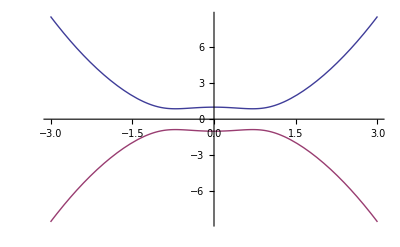

```mathematica
Plot[{Sqrt[(-1.0+k k)^2 + k k],-Sqrt[(-1.0+k k)^2 + k k]},{k,-3,3}]
```

```mathematica
Simplify[Solve[0==(M0+M k k 0 -M kz kz )^2+ A A k k 0- B B kz kz ,kz],Assumptions->{M>0}]
```

{{kz→-(B+√(B^2+4 M M0))/(2 M)},{kz→(B-√(B^2+4 M M0))/(2 M)},{kz→(-B+√(B^2+4 M M0))/(2 M)},{kz→(B+√(B^2+4 M M0))/(2 M)}}

```mathematica
TrigReduce[Sin[a]Sin[b]]
```

1/2 (Cos[a-b]-Cos[a+b])

```mathematica
Integrate[Cos[a x]Sin[b x],x]
```

Cos[(a-b) x]/(2 (a-b))-Cos[(a+b) x]/(2 (a+b))

```mathematica
Table[Exp[I π(p p -3p +1)/100],{p,0,10}]
Table[Exp[-I π(p p +4p +1)/100],{p,0,10}]
```

{ⅇ^((ⅈ π)/100),ⅇ^(-(ⅈ π)/100),ⅇ^(-(ⅈ π)/100),ⅇ^((ⅈ π)/100),ⅇ^((ⅈ π)/20),ⅇ^((11 ⅈ π)/100),ⅇ^((19 ⅈ π)/100),ⅇ^((29 ⅈ π)/100),ⅇ^((41 ⅈ π)/100),ⅇ^((11 ⅈ π)/20),ⅇ^((71 ⅈ π)/100)}

{ⅇ^(-(ⅈ π)/100),ⅇ^(-(3 ⅈ π)/50),ⅇ^(-(13 ⅈ π)/100),ⅇ^(-(11 ⅈ π)/50),ⅇ^(-(33 ⅈ π)/100),ⅇ^(-(23 ⅈ π)/50),ⅇ^(-(61 ⅈ π)/100),ⅇ^(-(39 ⅈ π)/50),ⅇ^(-(97 ⅈ π)/100),ⅇ^((41 ⅈ π)/50),ⅇ^((59 ⅈ π)/100)}

```mathematica
u=RandomReal[1,10];
v=RandomReal[1,10];
ListConvolve[u,v,{1,-1},0]
```

{0.594652,0.523177,0.156454,0.883763,0.685474,0.265582,0.525513,0.703307,0.835203,0.903549}

{0.811293,0.371564,0.404215,0.368862,0.0012882,0.558945,0.698263,0.89619,0.239177,0.944699}

{0.482437,0.645401,0.561691,1.20594,1.14148,1.21815,1.83594,2.11287,2.4645,3.3492,2.8842,2.12688,2.33127,2.14114,2.09511,2.04408,1.67393,1.00512,0.853582}

```mathematica
ll={1,2,3,4,5}
ListConvolve[ll,ll,{1,-1},0]
```

{1,2,3,4,5}

{1,4,10,20,35,44,46,40,25}

```mathematica
Integrate[Sin[m π x]Sin[n π x]Sin[p π x],{x,0,1}]
Integrate[Sin[2 π x]Sin[1 π x]Sin[1 π x],{x,0,1}]
```

1/(4 π)(1/(m+n-p)+1/(m-n+p)+1/(-m+n+p)-1/(m+n+p)+Cos[(m-n-p) π]/(m-n-p)-Cos[(m+n-p) π]/(m+n-p)-Cos[(m-n+p) π]/(m-n+p)+Cos[(m+n+p) π]/(m+n+p))

0

```mathematica
cosfun[m_]:=Which[m==0,0,m≠0,1/(2 π)(1/m-Cos[(m) π]/m)];
cosfun2[m_,n_,p_]:=cosfun[m+n-p]+cosfun[m-n+p]+cosfun[-m+n+p]-cosfun[m+n+p];(*1/(4 π)(1/(m+n-p)+1/(m-n+p)+1/(-m+n+p)-1/(m+n+p)+Cos[(m-n-p) π]/(m-n-p)-Cos[(m+n-p) π]/(m+n-p)-Cos[(m-n+p) π]/(m-n+p)+Cos[(m+n+p) π]/(m+n+p));*)
delta[u_,v_,NN_]:=Table[Sum[u[[n]]v[[m]]cosfun2[m,n,p],{n,NN},{m,NN}],{p,1,NN}]
u=RandomReal[1,20];
v=RandomReal[1,20];
ListConvolve[u,v,{1,-1},0]
delta[u,v,20]//N
```

{0.0648153,0.64624,0.506928,1.40453,1.83446,1.69085,2.06421,2.07948,1.76912,2.30219,2.3885,2.40769,2.55921,2.67423,2.25818,3.1543,3.76456,4.04586,5.14307,5.42798,4.27691,4.7474,3.65968,3.39504,2.99503,2.72014,2.70328,3.08045,2.3175,2.25715,2.39941,2.09779,2.06705,2.40006,2.08886,1.23931,1.23706,0.802608,0.364936}

{0.604147,2.1192,2.18394,2.30726,3.10672,2.44332,2.44504,2.54038,2.25756,2.19005,2.52651,2.33904,2.48048,3.16862,2.84294,3.422,3.87446,3.15641,2.88752,2.71064}

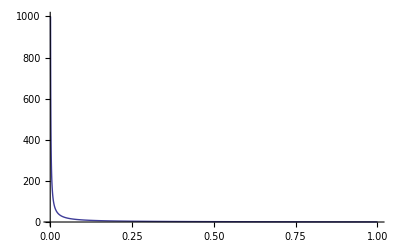

```mathematica
Plot[Cos[x]/x,{x,.001,1},PlotRange->All]
```

```mathematica
Integrate[Sin[1 π x]Sin[1 π x],{x,0,1}]
```

1/2

```mathematica
TrigReduce[Sin[a]Sin[b]]//TrigToExp
TrigReduce[Sin[c]]//TrigToExp
```

-1/4 ⅇ^(-ⅈ a-ⅈ b)+1/4 ⅇ^(ⅈ a-ⅈ b)+1/4 ⅇ^(-ⅈ a+ⅈ b)-1/4 ⅇ^(ⅈ a+ⅈ b)

1/2 ⅈ ⅇ^(-ⅈ c)-1/2 ⅈ ⅇ^(ⅈ c)

```mathematica
MatrixForm[Table[cosfun2[m,n,1],{m,1,5},{n,1,5}]]
```

(8/(3 π) | 0 | -8/(15 π) | 0 | -8/(105 π)
0 | 32/(15 π) | 0 | -64/(105 π) | 0
-8/(15 π) | 0 | 72/(35 π) | 0 | -40/(63 π)
0 | -64/(105 π) | 0 | 128/(63 π) | 0
-8/(105 π) | 0 | -40/(63 π) | 0 | 200/(99 π))

(ⅈ (-1)^n (-6+n^2 π^2) Sign[n]^4)/n^3

-(2 (-1)^n (-6+n^2 π^2))/n^3

(2 (-6+π^2) Sin[x]+(3/2-π^2) Sin[2 x]+2/9 (-2+3 π^2) Sin[3 x]+1/16 (3-8 π^2) Sin[4 x]+2/125 (-6+25 π^2) Sin[5 x]+1/18 (1-6 π^2) Sin[6 x]+2/343 (-6+49 π^2) Sin[7 x]) (2 (126-21 π^2+π^4) Sin[x]-(-3+π^2)^2 Sin[2 x]+2/81 (58-87 π^2+27 π^4) Sin[3 x]+1/64 (-27+72 π^2-32 π^4) Sin[4 x]+2/625 (54-225 π^2+125 π^4) Sin[5 x]+1/81 (-7+42 π^2-27 π^4) Sin[6 x]+(2 (414-3381 π^2+2401 π^4) Sin[7 x])/16807)

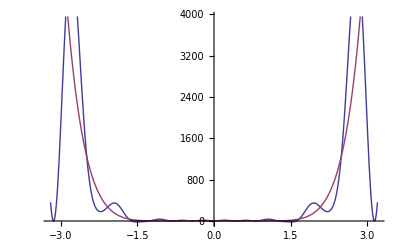

```mathematica
FourierCoefficient[x^3,x,n]
FourierSinCoefficient[x^3,x,n]
FourierSinSeries[x^3,x,7] FourierSinSeries[x x x x x-x x x,x,7]
Plot[{%,(x x x)( x x x x x-x x x)},{x,-3.2,3.2}]
```

{Sin[π x],Sin[2 π x],Sin[3 π x],Sin[4 π x],Sin[5 π x]}

{1/2 (1-Cos[2 π x]),Cos[π x]-Cos[3 π x],1/2 (1+2 Cos[2 π x]-3 Cos[4 π x]),Cos[π x]+Cos[3 π x]-2 Cos[5 π x],1/2 (1+2 Cos[2 π x]+2 Cos[4 π x]-5 Cos[6 π x]),Cos[π x]+Cos[3 π x]-2 Cos[7 π x],1/2 (1+2 Cos[2 π x]-3 Cos[8 π x]),Cos[π x]-Cos[9 π x],1/2 (1-Cos[10 π x])}

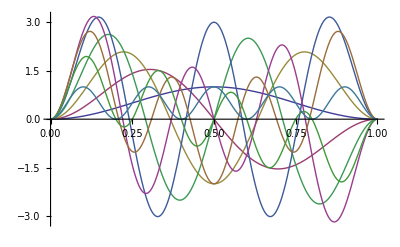

```mathematica
ss=Table[Sin[n π x],{n,1,5}]
ListConvolve[ss,ss,{1,-1},0]//TrigReduce
Plot[%,{x,0,1}]
```

```mathematica
Eigenvalues[{{( k k -1)μ,-I d},{I d,-( k k -1)μ}}]
```

{-√(d^2+μ^2-2 k^2 μ^2+k^4 μ^2),√(d^2+μ^2-2 k^2 μ^2+k^4 μ^2)}

```mathematica
{-√(d^2 k^2+μ^2-2 k^2 μ^2+k^4 μ^2),√(d^2 k^2+μ^2-2 k^2 μ^2+k^4 μ^2)}
```

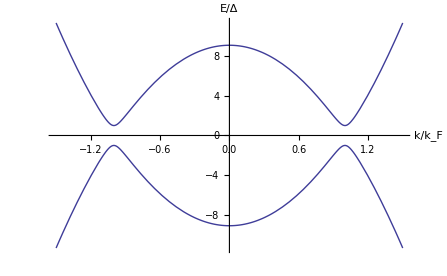

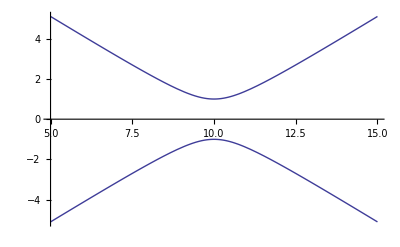

```mathematica
Plot[{-√(d^2+μ^2-2 k^2 μ^2+k^4 μ^2),√(d^2+μ^2-2 k^2 μ^2+k^4 μ^2)}/.{d->1,μ->9},{k,-1.5,1.5},AxesLabel->{"k/k_F","E/Δ"},PlotStyle->Thick]
Plot[{-√(d^2+k^2-2 k μ+μ^2),√(d^2+k^2-2 k μ+μ^2)}/.{d->1,μ->10},{k,5,15},AxesLabel->{k}]
```

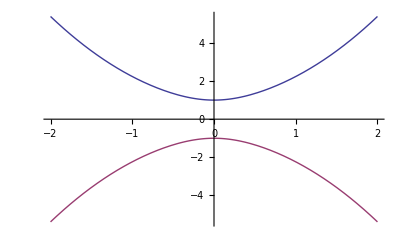

```mathematica
Plot[{Sqrt[(1.0+k k)^2 + k k],-Sqrt[(1.0+k k)^2 + k k]},{k,-2,2}]
```

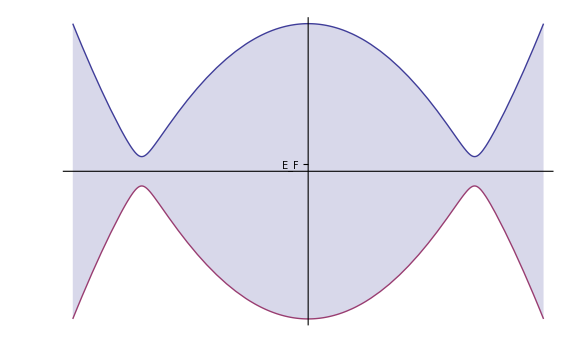

```mathematica
Plot[{Sqrt[(k k-2)^2+(.2)^2],-Sqrt[(k k-2)^2+(.2)^2] },{k,-2,2},Filling->{1->{2}},TicksStyle->{Directive[Black,30],Black},Ticks->{None,{{0.1,"E_F"}}},PlotStyle->{Thick,Thick,{Dashed,Thick,Red}},ImageSize->Large]
```

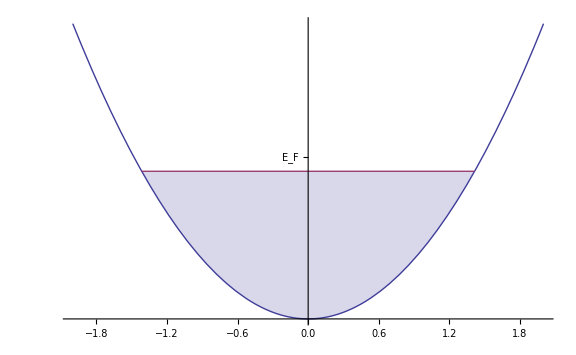

```mathematica
Show[%9,ImageSize->Large]
```

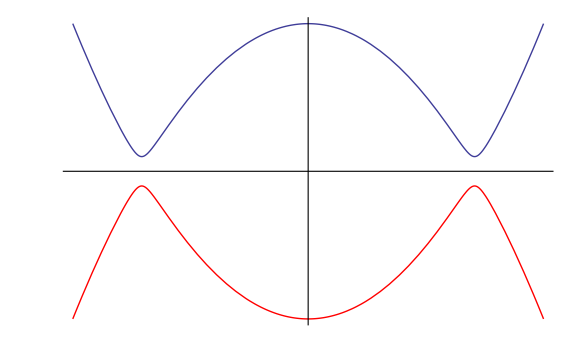

```mathematica
Plot[{Sqrt[(k k-2)^2+(.2)^2],-Sqrt[(k k-2)^2+(.2)^2] },{k,-2,2},Ticks->None,PlotStyle->{Thick,{Thick,Red}},ImageSize->Large]
```

```mathematica
Plot3D[{-Sqrt[kx kx +ky ky],Sqrt[kx kx +ky ky]},{kx,-1,1},{ky,-1,1},ColorFunction->"Rainbow",BoxRatios->{1,1,2},Ticks->{{0,1},{-1,0,1},{-1,0,1}},AxesLabel->{"ℏv_Fk_x","ℏv_Fk_y","E(eV)"},LabelStyle->Directive[20]]
ℏ
```

-Graphics3D-

ℏ

```mathematica
L
```

```mathematica
Eigenvalues[{{( k k -1)μ,-I d k Exp[I ϕ]},{I d k Exp[-I ϕ],-( k k -1)μ}}]
```

{-√(d^2 k^2+μ^2-2 k^2 μ^2+k^4 μ^2),√(d^2 k^2+μ^2-2 k^2 μ^2+k^4 μ^2)}

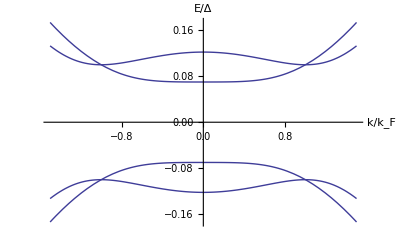

```mathematica
Plot[{-√(d^2 k^2+μ^2-2 k^2 μ^2+k^4 μ^2),√(d^2 k^2+μ^2-2 k^2 μ^2+k^4 μ^2),-√(d^2+μ^2-2 k^2 μ^2+k^4 μ^2),√(d^2+μ^2-2 k^2 μ^2+k^4 μ^2)}/.{d->.1,μ->.07},{k,-1.5,1.5},AxesLabel->{"k/k_F","E/Δ"},PlotStyle->Thick]
```

```mathematica
H={{0,ky+I kx},{ky-I kx,0}};
Eigensystem[H]
H={{0,k Sin[θ]+I k Cos[θ]},{k Sin[θ]-I k Cos[θ],0}};
Eigensystem[H][[2]]//MatrixForm
```

{{-√(kx^2+ky^2),√(kx^2+ky^2)},{{-(ⅈ √(kx^2+ky^2))/(kx+ⅈ ky),1},{(ⅈ √(kx^2+ky^2))/(kx+ⅈ ky),1}}}

(-ⅈ (Cos[θ]-ⅈ Sin[θ]) | 1
ⅈ (Cos[θ]-ⅈ Sin[θ]) | 1)

```mathematica
H1=λ J {{0,Exp[-I(-kx +√3 ky)/2]},{Exp[I(-kx +√3 ky)/2],0}}+ J {{0,Exp[-I(-kx -√3 ky)/2]},{Exp[I(-kx -√3 ky)/2],0}}+ J {{0,Exp[-I(kx )]},{Exp[I(kx )],0}};
H2= J {{0,Exp[-I(-kx +√3 ky)/2]},{Exp[I(-kx +√3 ky)/2],0}}+ λ J {{0,Exp[-I(-kx -√3 ky)/2]},{Exp[I(-kx -√3 ky)/2],0}}+ J {{0,Exp[-I(kx )]},{Exp[I(kx )],0}};
H3= J {{0,Exp[-I(-kx +√3 ky)/2]},{Exp[I(-kx +√3 ky)/2],0}}+ J {{0,Exp[-I(-kx -√3 ky)/2]},{Exp[I(-kx -√3 ky)/2],0}}+ λ J {{0,Exp[-I(kx )]},{Exp[I(kx )],0}};

MatrixExp[-I H3]//FullSimplify
H1=X1 σx +Y1 σy;
H2=X2 σx +Y2 σy;
H3=X3 σx +Y3 σy;
MatrixExp[-I H1].MatrixExp[-I H2].MatrixExp[-I H3]//Simplify
```

{{Cos[ⅇ^(-1/4 ⅈ (3 kx+2 √3 ky)) J √(ⅇ^(1/2 ⅈ (3 kx+2 √3 ky)) (2+λ^2+4 λ Cos[(3 kx)/2] Cos[(√3 ky)/2]+2 Cos[√3 ky]))],-(ⅈ ⅇ^(-(ⅈ kx)/4) (ⅇ^((3 ⅈ kx)/2)+ⅇ^((3 ⅈ kx)/2+ⅈ √3 ky)+ⅇ^(1/2 ⅈ √3 ky) λ) Sin[ⅇ^(-1/4 ⅈ (3 kx+2 √3 ky)) J √(ⅇ^(1/2 ⅈ (3 kx+2 √3 ky)) (2+λ^2+4 λ Cos[(3 kx)/2] Cos[(√3 ky)/2]+2 Cos[√3 ky]))])/(√(ⅇ^(1/2 ⅈ (3 kx+2 √3 ky)) (2+λ^2+4 λ Cos[(3 kx)/2] Cos[(√3 ky)/2]+2 Cos[√3 ky])))},{-(ⅈ ⅇ^((ⅈ kx)/4) (1+ⅇ^(ⅈ √3 ky)+ⅇ^(1/2 ⅈ (3 kx+√3 ky)) λ) Sin[ⅇ^(-1/4 ⅈ (3 kx+2 √3 ky)) J √(ⅇ^(1/2 ⅈ (3 kx+2 √3 ky)) (2+λ^2+4 λ Cos[(3 kx)/2] Cos[(√3 ky)/2]+2 Cos[√3 ky]))])/(√(ⅇ^(1/2 ⅈ (3 kx+2 √3 ky)) (2+λ^2+4 λ Cos[(3 kx)/2] Cos[(√3 ky)/2]+2 Cos[√3 ky]))),Cos[ⅇ^(-1/4 ⅈ (3 kx+2 √3 ky)) J √(ⅇ^(1/2 ⅈ (3 kx+2 √3 ky)) (2+λ^2+4 λ Cos[(3 kx)/2] Cos[(√3 ky)/2]+2 Cos[√3 ky]))]}}

MatrixExp[-ⅈ (X1 σx+Y1 σy)].MatrixExp[-ⅈ (X2 σx+Y2 σy)].MatrixExp[-ⅈ (X3 σx+Y3 σy)]

```mathematica
H1=λ J {{0,Sin[I(-kx +√3 ky)/2]},{Exp[I(-kx +√3 ky)/2],0}}+ J {{0,Sin[I(-kx -√3 ky)/2]},{Exp[I(-kx -√3 ky)/2],0}}+ J {{0,Sin[I(kx )]},{Exp[I(kx )],0}};
H1=λ J {{0,Exp[-I(-kx +√3 ky)/2]},{Exp[I(-kx +√3 ky)/2],0}}+ J {{0,Exp[-I(-kx -√3 ky)/2]},{Exp[I(-kx -√3 ky)/2],0}}+ J {{0,Exp[-I(kx )]},{Exp[I(kx )],0}};
(λ Sin[(-kx +√3 ky)/2]+Sin[(-kx -√3 ky)/2]+Sin[(kx )])^2+(λ Cos[(-kx +√3 ky)/2]+Cos[(-kx -√3 ky)/2]+Cos[(kx )])^2//Expand//Simplify
( Sin[(-kx +√3 ky)/2]+λ Sin[(-kx -√3 ky)/2]+Sin[(kx )])^2+( Cos[(-kx +√3 ky)/2]+λ Cos[(-kx -√3 ky)/2]+Cos[(kx )])^2//Expand//Simplify
( Sin[(-kx +√3 ky)/2]+Sin[(-kx -√3 ky)/2]+λ Sin[(kx )])^2+( Cos[(-kx +√3 ky)/2]+Cos[(-kx -√3 ky)/2]+λ Cos[(kx )])^2//Expand//Simplify
```

2+λ^2+2 λ Cos[√3 ky]+2 λ Cos[1/2 (3 kx-√3 ky)]+2 Cos[1/2 (3 kx+√3 ky)]

2+λ^2+2 λ Cos[√3 ky]+2 Cos[1/2 (3 kx-√3 ky)]+2 λ Cos[1/2 (3 kx+√3 ky)]

2+λ^2+2 Cos[√3 ky]+2 λ Cos[1/2 (3 kx-√3 ky)]+2 λ Cos[1/2 (3 kx+√3 ky)]

```mathematica
σ0=PauliMatrix[0];
σx=PauliMatrix[1];
σy=PauliMatrix[2];
σz=PauliMatrix[3];
(Cos[θ1] σ0 + I Sin[θ1](X1 σx +Y1 σy)/n1);
(Cos[θ2] σ0 + I Sin[θ2](X2 σx +Y2 σy)/n2);
(Cos[θ3] σ0 + I Sin[θ3](X3 σx +Y3 σy)/n3);
U1={{Cos[θ1],ⅈ Exp[-I ϕ1] Sin[θ1]},{ⅈ Exp[I ϕ1] Sin[θ1],Cos[θ1]}}
U2={{Cos[θ2],ⅈ Exp[-I ϕ2] Sin[θ2]},{ⅈ Exp[I ϕ2] Sin[θ2],Cos[θ2]}}
U3={{Cos[θ3],ⅈ Exp[-I ϕ3] Sin[θ3]},{ⅈ Exp[I ϕ3] Sin[θ3],Cos[θ3]}}
U1.U2.U3//Simplify//MatrixForm
```

{{Cos[θ1],ⅈ ⅇ^(-ⅈ ϕ1) Sin[θ1]},{ⅈ ⅇ^(ⅈ ϕ1) Sin[θ1],Cos[θ1]}}

{{Cos[θ2],ⅈ ⅇ^(-ⅈ ϕ2) Sin[θ2]},{ⅈ ⅇ^(ⅈ ϕ2) Sin[θ2],Cos[θ2]}}

{{Cos[θ3],ⅈ ⅇ^(-ⅈ ϕ3) Sin[θ3]},{ⅈ ⅇ^(ⅈ ϕ3) Sin[θ3],Cos[θ3]}}

(-ⅇ^(-ⅈ ϕ1) Sin[θ1] (ⅇ^(ⅈ ϕ2) Cos[θ3] Sin[θ2]+ⅇ^(ⅈ ϕ3) Cos[θ2] Sin[θ3])+Cos[θ1] (Cos[θ2] Cos[θ3]-ⅇ^(-ⅈ (ϕ2-ϕ3)) Sin[θ2] Sin[θ3]) | ⅈ (Cos[θ3] (ⅇ^(-ⅈ ϕ1) Cos[θ2] Sin[θ1]+ⅇ^(-ⅈ ϕ2) Cos[θ1] Sin[θ2])+ⅇ^(-ⅈ ϕ3) (Cos[θ1] Cos[θ2]-ⅇ^(-ⅈ (ϕ1-ϕ2)) Sin[θ1] Sin[θ2]) Sin[θ3])
ⅈ Cos[θ3] (ⅇ^(ⅈ ϕ1) Cos[θ2] Sin[θ1]+ⅇ^(ⅈ ϕ2) Cos[θ1] Sin[θ2])+ⅈ ⅇ^(ⅈ ϕ3) (Cos[θ1] Cos[θ2]-ⅇ^(ⅈ (ϕ1-ϕ2)) Sin[θ1] Sin[θ2]) Sin[θ3] | Cos[θ3] (Cos[θ1] Cos[θ2]-ⅇ^(ⅈ (ϕ1-ϕ2)) Sin[θ1] Sin[θ2])-ⅇ^(-ⅈ ϕ3) (ⅇ^(ⅈ ϕ1) Cos[θ2] Sin[θ1]+ⅇ^(ⅈ ϕ2) Cos[θ1] Sin[θ2]) Sin[θ3])

```mathematica
data=Table[If[(x x + y y-.8<0)&&(x x + y y-.6>0),{y,-x,0},{0,0,0}],{x,-1,1,.01},{y,-1,1,.01},{z,0,1,1}];
ListVectorPlot3D[data(*,DataRange->{{-2,2},{-2,2}}*),VectorStyle->"Arrow3D",AspectRatio->2]
```

-Graphics3D-

```mathematica
vectors = Table[{y,-x,0},{x,-1,1,.1},{y,-1,1,.1},{z,-1,1,1}];ListVectorPlot3D[vectors]
```

-Graphics3D-

```mathematica
Solve[-7/(.001*8.988) == -24/(x x) + 40/(x-.2)^2, x]
Solve[-7/(.001*8.988) == 24/(x x) - 40/(x-.2)^2, x]
Solve[-7/(.001*8.988) == 24/(x x) + 40/(x-.2)^2, x]
```

{{x→-0.146972},{x→0.0813968},{x→0.232788-0.221014 ⅈ},{x→0.232788+0.221014 ⅈ}}

{{x→-0.0508356-0.172394 ⅈ},{x→-0.0508356+0.172394 ⅈ},{x→0.0934797},{x→0.408191}}

{{x→0.0486583-0.117119 ⅈ},{x→0.0486583+0.117119 ⅈ},{x→0.151342-0.2318 ⅈ},{x→0.151342+0.2318 ⅈ}}